```mathematica
SetDirectory["/Users/vsvh/docs/research/comm_patterns_git"]
```

/Users/vsvh/docs/research/comm_patterns_git

```mathematica
data = Import["/Users/vsvh/docs/research/commpatterns/data/contour.dat"]
```

{{0,0,1.},{0,1,1.},{0,2,1.},{0,3,1.},{0,4,0.848765},{0,5,0.725309},{0,6,0.615741},{0,7,0.584877},{0,8,0.544753},{0,9,0.506173},{0,10,0.481481},{0,11,0.447531},{0,12,0.41821},{0,13,0.376543},{0,14,0.337963},{0,15,0.291667},{0,16,0.223765},{0,17,0.166667},{0,18,0.118827},{0,19,0.070988},{0,20,0.007716},{1,0,1.},{1,1,1.},{1,2,1.},{1,3,1.},{1,4,0.919105},{1,5,0.824441},{1,6,0.736661},{1,7,0.703959},{1,8,0.667814},{1,9,0.636833},{1,10,0.593804},{1,11,0.569707},{1,12,0.521515},{1,13,0.444062},{1,14,0.383821},{1,15,0.321859},{1,16,0.251291},{1,17,0.185886},{1,18,0.134251},{1,19,0.079174},{1,20,0.008606},{2,0,1.},{2,1,1.},{2,2,1.},{2,3,1.},{2,4,0.958237},{2,5,0.911833},{2,6,0.837587},{2,7,0.791183},{2,8,0.767981},{2,9,0.726218},{2,10,0.682135},{2,11,0.663573},{2,12,0.645012},{2,13,0.584687},{2,14,0.515081},{2,15,0.450116},{2,16,0.37355},{2,17,0.264501},{2,18,0.167053},{2,19,0.090487},{2,20,0.018561},{3,0,1.},{3,1,1.},{3,2,1.},{3,3,1.},{3,4,0.990476},{3,5,0.957143},{3,6,0.890476},{3,7,0.852381},{3,8,0.828571},{3,9,0.8},{3,10,0.771429},{3,11,0.742857},{3,12,0.714286},{3,13,0.7},{3,14,0.638095},{3,15,0.580952},{3,16,0.452381},{3,17,0.252381},{3,18,0.157143},{3,19,0.104762},{3,20,0.004762},{4,0,1.},{4,1,1.},{4,2,1.},{4,3,1.},{4,4,0.98913},{4,5,0.956522},{4,6,0.934783},{4,7,0.902174},{4,8,0.880435},{4,9,0.869565},{4,10,0.847826},{4,11,0.826087},{4,12,0.804348},{4,13,0.76087},{4,14,0.728261},{4,15,0.684783},{4,16,0.565217},{4,17,0.402174},{4,18,0.271739},{4,19,0.173913},{4,20,0.043478}}

```mathematica
{{0,0,1.},{0,1,1.},{0,2,1.},{0,3,1.},{0,4,0.848765},{0,5,0.725309},{0,6,0.615741},{0,7,0.584877},{0,8,0.544753},{0,9,0.506173},{0,10,0.481481},{0,11,0.447531},{0,12,0.41821},{0,13,0.376543},{0,14,0.337963},{0,15,0.291667},{0,16,0.223765},{0,17,0.166667},{0,18,0.118827},{0,19,0.070988},{0,20,0.007716},{1,0,1.},{1,1,1.},{1,2,1.},{1,3,1.},{1,4,0.919105},{1,5,0.824441},{1,6,0.736661},{1,7,0.703959},{1,8,0.667814},{1,9,0.636833},{1,10,0.593804},{1,11,0.569707},{1,12,0.521515},{1,13,0.444062},{1,14,0.383821},{1,15,0.321859},{1,16,0.251291},{1,17,0.185886},{1,18,0.134251},{1,19,0.079174},{1,20,0.008606},{2,0,1.},{2,1,1.},{2,2,1.},{2,3,1.},{2,4,0.958237},{2,5,0.911833},{2,6,0.837587},{2,7,0.791183},{2,8,0.767981},{2,9,0.726218},{2,10,0.682135},{2,11,0.663573},{2,12,0.645012},{2,13,0.584687},{2,14,0.515081},{2,15,0.450116},{2,16,0.37355},{2,17,0.264501},{2,18,0.167053},{2,19,0.090487},{2,20,0.018561},{3,0,1.},{3,1,1.},{3,2,1.},{3,3,1.},{3,4,0.990476},{3,5,0.957143},{3,6,0.890476},{3,7,0.852381},{3,8,0.828571},{3,9,0.8},{3,10,0.771429},{3,11,0.742857},{3,12,0.714286},{3,13,0.7},{3,14,0.638095},{3,15,0.580952},{3,16,0.452381},{3,17,0.252381},{3,18,0.157143},{3,19,0.104762},{3,20,0.004762},{4,0,1.},{4,1,1.},{4,2,1.},{4,3,1.},{4,4,0.98913},{4,5,0.956522},{4,6,0.934783},{4,7,0.902174},{4,8,0.880435},{4,9,0.869565},{4,10,0.847826},{4,11,0.826087},{4,12,0.804348},{4,13,0.76087},{4,14,0.728261},{4,15,0.684783},{4,16,0.565217},{4,17,0.402174},{4,18,0.271739},{4,19,0.173913},{4,20,0.043478}}
```

```mathematica
points0 = Import["/Users/vsvh/docs/research/commpatterns/data/points0.dat"]
```

{{0,19},{0,20},{1,19},{1,20},{2,20},{3,19},{4,18},{4,19},{4,20}}

```mathematica
points1 = Import["/Users/vsvh/docs/research/commpatterns/data/points1.dat"]
```

{{0,17},{0,18},{1,18},{2,18},{2,19},{3,18}}

{{0,0},{0,1},{0,2},{0,3},{1,0},{1,1},{1,2},{1,3},{1,4},{2,0},{2,1},{2,2},{2,3},{2,4},{2,5},{3,0},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{4,0},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14}}

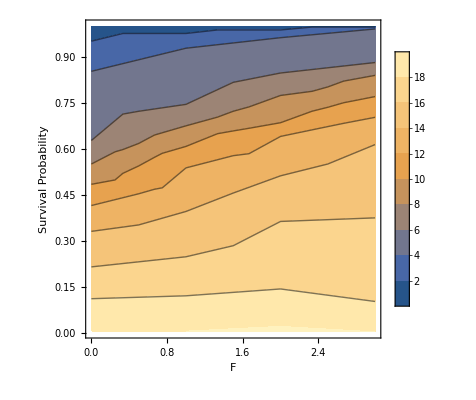

```mathematica
points2 = Import["/Users/vsvh/docs/research/commpatterns/data/points2.dat"];
points3 = Import["/Users/vsvh/docs/research/commpatterns/data/points3.dat"];
points4 = Import["/Users/vsvh/docs/research/commpatterns/data/points4.dat"];
points5 = Import["/Users/vsvh/docs/research/commpatterns/data/points5.dat"];
points6 = Import["/Users/vsvh/docs/research/commpatterns/data/points6.dat"];
points7 = Import["/Users/vsvh/docs/research/commpatterns/data/points7.dat"];
points8 = Import["/Users/vsvh/docs/research/commpatterns/data/points8.dat"];
points9 = Import["/Users/vsvh/docs/research/commpatterns/data/points9.dat"]
```

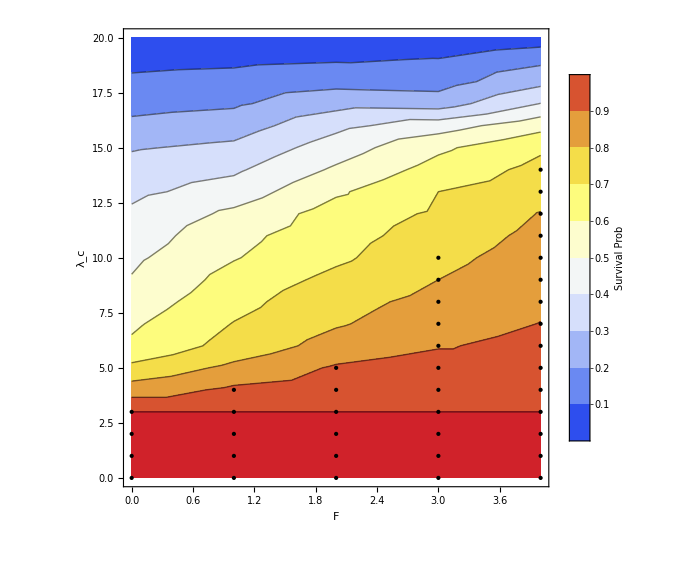

Thread::tdlen: Objects of unequal length in {{\"\<x\>\", \"\<y\>\", \"\<z\>\"}, {1, 1., 0}, {2, 1., 0}, {3, 1., 0}, {4, 0.852853, 0}, {5, 0.732733, 0}, {6, 0.627628, 0}, {7, 0.593093, 0}, {8, 0.551051, 0}, {9, 0.512012, 0}, «71»}\\\ {1} cannot be combined.

```mathematica
pc = ListContourPlot[data,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ Italic,FontFamily->"Helvetica", FontSize->20}],Right], FrameLabel->{"F","\[\Lambda]_c"}, LabelStyle->{FontFamily->"Helvetica", FontSize->18}, ImageSize->Large, ColorFunction->"TemperatureMap", Epilog->{PointSize[Large],Black,Point[points9]}]
```

```mathematica
Export["~/tmp/contour.png", pc]
```

~/tmp/contour.png

```mathematica
ColorData["Gradients"][1]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}[1]

```mathematica
ListContourPlot[data,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Survival Prob",LabelStyle->{ Italic,FontFamily->"Helvetica", FontSize->20}],Right], FrameLabel->{"F","\[\Lambda]_c"}, LabelStyle->{FontFamily->"Helvetica", FontSize->18}, ImageSize->Large, ColorFunction->"BrownCyanTones", Epilog->{PointSize[Large],ColorData["BrownCyanTones"][0.1],Point[points1]}]
```